```mathematica
Transpose[ConversionMatrix["G","C"]]==ConversionMatrix["E","C"]
```

True

```mathematica
Table[Labeled[Det[ConversionMatrix[base1,base2]],base1->base2],{base1,Keys[Bases]},{base2,Keys[Bases]}]
```

{{1C→C,1C→E,1C→G,-1/195689447424C→F,1C→T},{1E→C,1E→E,1E→G,-1/195689447424E→F,1E→T},{1G→C,1G→E,1G→G,-1/195689447424G→F,1G→T},{-195689447424F→C,-195689447424F→E,-195689447424F→G,1F→F,-195689447424F→T},{1T→C,1T→E,1T→G,-1/195689447424T→F,1T→T}}

```mathematica
FactorInteger[195689447424]
```

{{2,28},{3,6}}

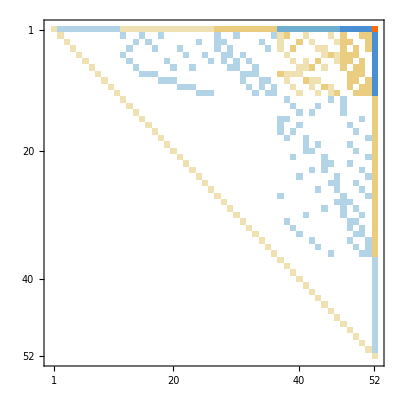

```mathematica
MatrixPlot[ConversionMatrix["C","E"]]
```

```mathematica
Monitor[Table[{base,Total[Table[Length[ListofVars[allGraphs5[k,Bases[base,"Colofour"]]]],{k,Keys[allGraphs5]}]]},{base,Keys[Bases]}],{base,k}]
```

{{C,15926},{E,26778},{G,18766},{F,59016},{T,20518}}

```mathematica
FactorInteger[26778]
```

{{2,1},{3,1},{4463,1}}

```mathematica
Bases["C"]
```

<|Colofour→colofour,AtomKeys→{29524,29525,29533,29527,29767,29605,29551,49207,36085,31711,30253,29768,29608,29560,49208,49216,49210,36086,36166,36112,31714,31954,31738,30262,30496,30334,29537,29857,29797,29633,56011,51475,49963,38281,36817,32441,49220,56012,51478,49972,36194,38308,36898,31984,32684,30586,29888,58288,56770,52232,39014,59048},Variables→{v1x2x3x4x5,v1x2x3x45,v1x2x34x5,v1x2x35x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x45,v1x24x35,v1x25x34,v12x3x45,v12x34x5,v12x35x4,v13x2x45,v13x24x5,v13x25x4,v14x2x35,v14x23x5,v14x25x3,v15x2x34,v15x23x4,v15x24x3,v1x2x345,v1x234x5,v1x235x4,v1x245x3,v123x4x5,v124x3x5,v125x3x4,v134x2x5,v135x2x4,v145x2x3,v12x345,v123x45,v124x35,v125x34,v13x245,v134x25,v135x24,v14x235,v145x23,v15x234,v1x2345,v1234x5,v1235x4,v1245x3,v1345x2,v12345}|>

```mathematica
ZeroOne[mat_]:=Map[Map[If[#≠0,1,0]&,#]&,mat]
```

```mathematica
Zero
```

Zero

```mathematica
ZeroOne[ConversionMatrix["C","G"]]==ZeroOne[ConversionMatrix["E","F"]]
```

True

```mathematica
SubMatrix[big_,small_]:=Block[{i,j},
For[i=1,i≤ Length[big],i++,
For[j=1,j≤ Length[big],j++,
If[small[[i,j]]>big[[i,j]],Return[False]]
]
];
Return [True];
]
```

```mathematica
SubMatrix[ZeroOne[ConversionMatrix["C","E"]],ZeroOne[ConversionMatrix["C","T"]]]
```

True

```mathematica
Table[SubMatrix[ZeroOne[ConversionMatrix["C","E"]],Transpose[ZeroOne[ConversionMatrix[base1,base2]]]],{base1,Keys[Bases]},{base2,Keys[Bases]}]//TableForm
```

True | False | True | False | False
False | True | False | True | False
True | False | True | False | False
False | True | False | True | False
False | False | False | False | True

```mathematica
Table[SubMatrix[ZeroOne[ConversionMatrix["C","E"]],ZeroOne[ConversionMatrix[base1,base2]]],{base1,Keys[Bases]},{base2,Keys[Bases]}]//TableForm
```

True | True | False | False | True
True | True | False | False | True
False | False | True | False | False
False | False | False | True | False
True | True | False | False | True

```mathematica
Boole[True]
```

1

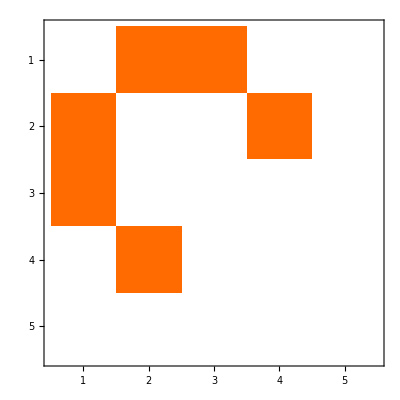

```mathematica
Table[Boole[
Or[
Equal[ZeroOne[ConversionMatrix["C","E"]],Transpose[ZeroOne[ConversionMatrix[base1,base2]]]],
Equal[ZeroOne[ConversionMatrix["C","E"]],ZeroOne[ConversionMatrix[base1,base2]]]
]
],{base1,Keys[Bases]},{base2,Keys[Bases]}]//MatrixPlot
```

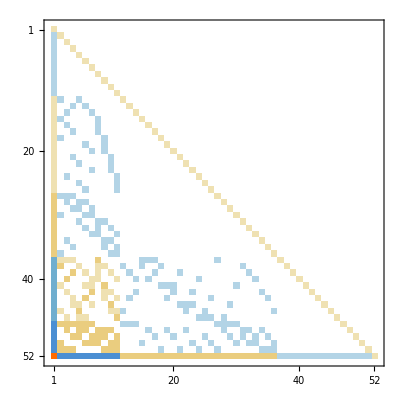

```mathematica
ConversionMatrix["C","E"].ConversionMatrix["E","G"]//MatrixPlot
```

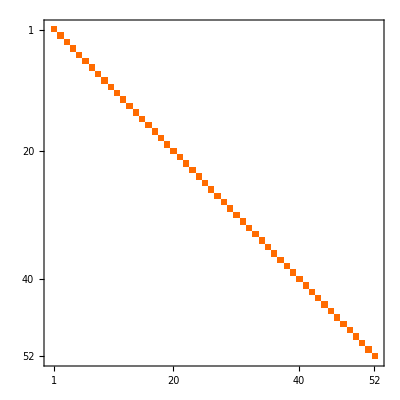
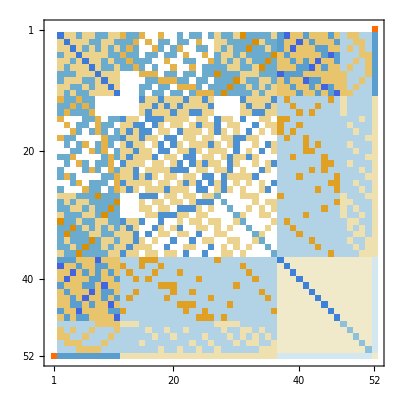
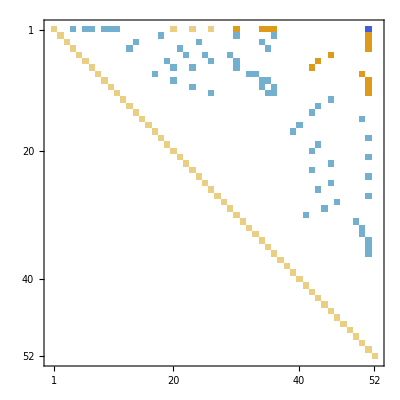
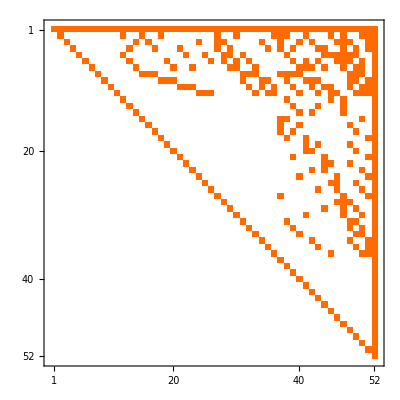
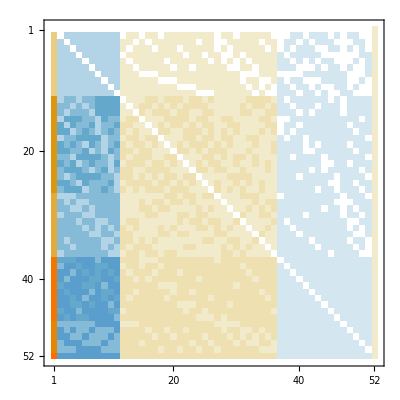
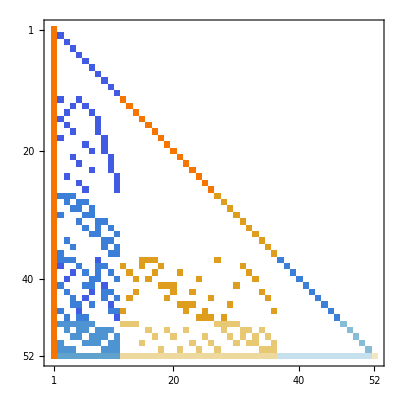
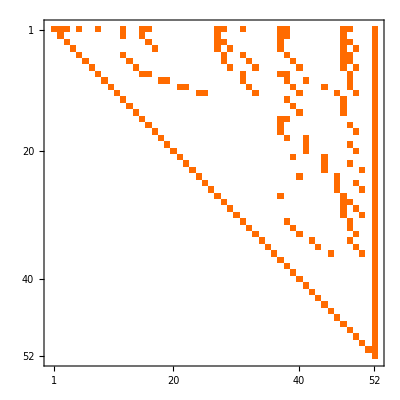
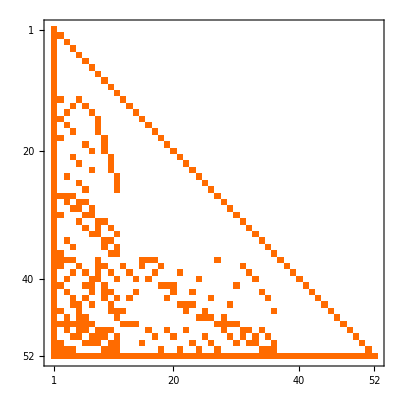
{{-Graphics-C→C,-Graphics-C→E,-Graphics-C→G,-Graphics-C→F,-Graphics-C→T},{-Graphics-E→C,-Graphics-E→E,-Graphics-E→G,-Graphics-E→F,-Graphics-E→T},{-Graphics-G→C,-Graphics-G→E,-Graphics-G→G,-Graphics-G→F,-Graphics-G→T},{-Graphics-F→C,-Graphics-F→E,-Graphics-F→G,-Graphics-F→F,-Graphics-F→T},{-Graphics-T→C,-Graphics-T→E,-Graphics-T→G,-Graphics-T→F,-Graphics-T→T}}

```mathematica
Table[Labeled[MatrixPlot[ConversionMatrix[base1,base2]],base1->base2],{base1,Keys[Bases]},{base2,Keys[Bases]}]
```

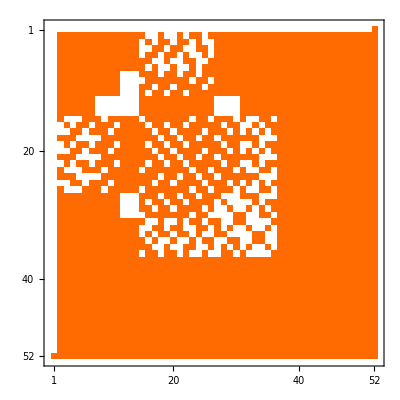
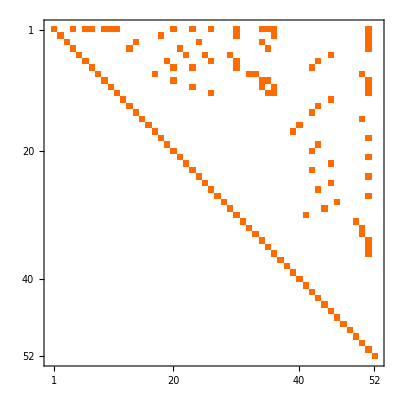
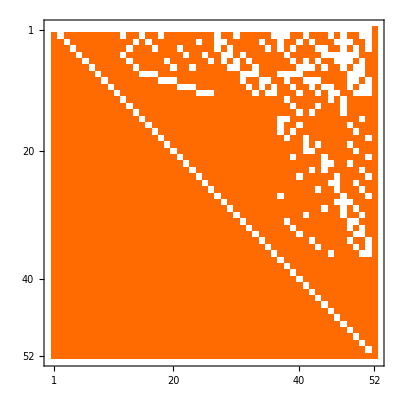
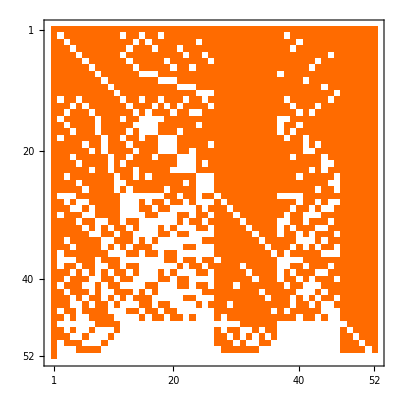
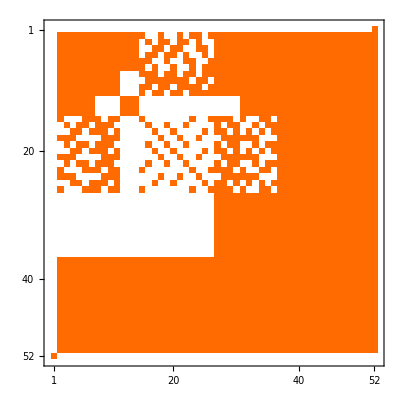
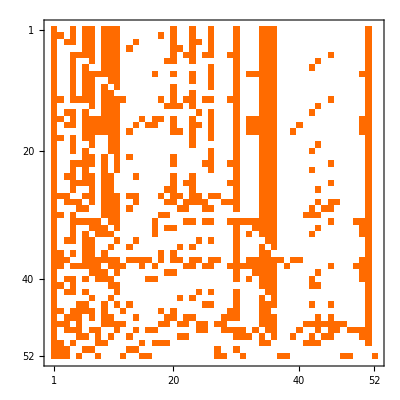
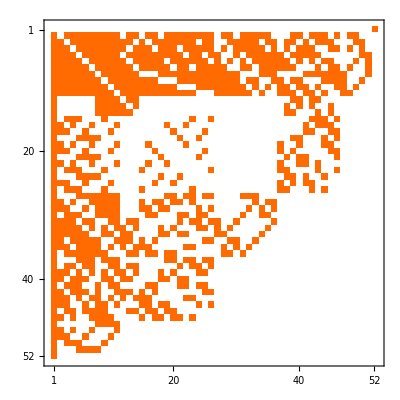
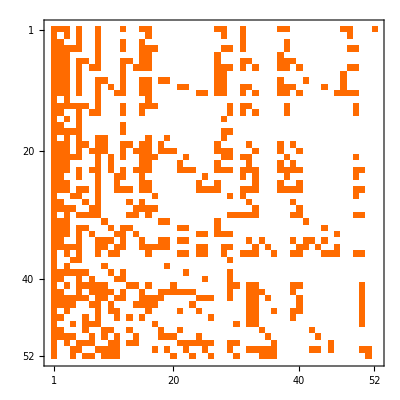
{{-Graphics-C→C,-Graphics-C→E,-Graphics-C→G,-Graphics-C→F,-Graphics-C→T},{-Graphics-E→C,-Graphics-E→E,-Graphics-E→G,-Graphics-E→F,-Graphics-E→T},{-Graphics-G→C,-Graphics-G→E,-Graphics-G→G,-Graphics-G→F,-Graphics-G→T},{-Graphics-F→C,-Graphics-F→E,-Graphics-F→G,-Graphics-F→F,-Graphics-F→T},{-Graphics-T→C,-Graphics-T→E,-Graphics-T→G,-Graphics-T→F,-Graphics-T→T}}

```mathematica
Table[Labeled[MatrixPlot[ZeroOne[ConversionMatrix[base1,base2]]],base1->base2],{base1,Keys[Bases]},{base2,Keys[Bases]}]
```

```mathematica
Table[Total[Flatten[ZeroOne[ConversionMatrix[base1,base2]]]],{base1,Keys[Bases]},{base2,Keys[Bases]}]//MatrixForm
```

(52 | 358 | 358 | 2258 | 131
358 | 52 | 2398 | 358 | 227
358 | 1938 | 52 | 1942 | 882
1153 | 358 | 862 | 52 | 719
131 | 227 | 578 | 2653 | 52)

```mathematica
52*52
```

2704

```mathematica
FactorInteger[535136149677240]
```

{{2,3},{3,2},{5,1},{41,1},{43,1},{229,1},{3681917,1}}

```mathematica
Monitor[Table[{base,Table[Total[Table[If[MemberQ[ListofVars[allGraphs5[k,Bases[base,"Colofour"]]],v],1,0],{k,Keys[allGraphs5]}]],{v,Bases[base,"Variables"]}]},{base,Keys[Bases]}],{base,v,k}]
```

{{C,{1024,576,576,576,576,576,576,576,576,576,576,328,328,328,328,328,328,328,328,328,328,328,328,328,328,328,232,232,232,232,232,232,232,232,232,232,138,138,138,138,138,138,138,138,138,138,94,94,94,94,94,52}},{E,{1024,576,576,576,576,576,576,576,576,576,576,328,328,328,328,328,328,328,328,328,328,328,328,328,328,328,616,616,616,616,616,616,616,616,616,616,354,354,354,354,354,354,354,354,354,354,830,830,830,830,830,1224}},{G,{1369,696,696,696,696,696,696,696,696,696,696,367,367,367,367,367,367,367,367,367,367,367,367,367,367,367,260,260,260,260,260,260,260,260,260,260,170,170,170,170,170,170,170,170,170,170,116,116,116,116,116,52}},{F,{52,1211,1211,1211,1211,1211,1211,1211,1211,1211,1211,1071,1071,1071,1071,1071,1071,1071,1071,1071,1071,1071,1071,1071,1071,1071,1128,1128,1128,1128,1128,1128,1128,1128,1128,1128,1227,1227,1227,1227,1227,1227,1227,1227,1227,1227,1203,1203,1203,1203,1203,1224}},{T,{1024,576,576,576,576,576,576,576,576,576,576,328,328,328,328,328,328,328,328,328,328,328,328,328,328,328,232,232,488,616,232,488,488,616,616,616,138,138,282,282,138,354,354,138,354,138,94,94,238,566,830,52}}}

```mathematica
Monitor[Table[{base,Table[Total[Table[If[MemberQ[ListofVars[allGraphs5[k,Bases[base,"Colofour"]]],v],1,0],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]],{v,Bases[base,"Variables"]}]},{base,Keys[Bases]}],{base,v,k}]
```

{{C,{1024,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,128,128,128,128,128,128,128,128,128,128,64,64,64,64,64,64,64,64,64,64,16,16,16,16,16,1}},{E,{1024,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,608,608,608,608,608,728}},{G,{608,292,292,292,292,292,292,292,292,292,292,156,156,156,156,156,156,156,156,156,156,156,156,156,156,156,64,64,64,64,64,64,64,64,64,64,63,63,63,63,63,63,63,63,63,63,15,15,15,15,15,1}},{F,{1,643,643,643,643,643,643,643,643,643,643,583,583,583,583,583,583,583,583,583,583,583,583,583,583,583,637,637,637,637,637,637,637,637,637,637,719,719,719,719,719,719,719,719,719,719,693,693,693,693,693,728}},{T,{1024,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,128,128,384,512,128,384,384,512,512,512,64,64,192,192,64,256,256,64,256,64,16,16,112,384,608,1}}}

```mathematica
Total[{1024,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,128,128,128,128,128,128,128,128,128,128,64,64,64,64,64,64,64,64,64,64,16,16,16,16,16,1}]
```

11985

```mathematica
Total[{1024,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,608,608,608,608,608,728}]
```

21432

```mathematica
Total[{1,643,643,643,643,643,643,643,643,643,643,583,583,583,583,583,583,583,583,583,583,583,583,583,583,583,637,637,637,637,637,637,637,637,637,637,719,719,719,719,719,719,719,719,719,719,693,693,693,693,693,728}]
```

32929

```mathematica
Total[{1024,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,128,128,384,512,128,384,384,512,512,512,64,64,192,192,64,256,256,64,256,64,16,16,112,384,608,1}]
```

16177